# Homework 3

Name: Eslam Muhammed Ahmed Zenhom

ID: 201700788

## Problem 1

```mathematica
ClearAll["Global`*"];
y=1;
n=5;
For[i=1,i≤n,++i,y=y*i] ;
nfactorial=y 
nfactorial==n!   (*the solution is verfied by this example*)

x=1;
n=5;
For[i=1,i≤(2n-1),i=i+2,x=x*i]
x
(2n-1)!!==x  (*the solution is verfied by this example*)

(*The bionmial cooefcient is ({{a}, {b}})*)
z=1;
h=1;
a=5;
b=3;
For[i=a-b+1,i≤a,++i,z=z*i];
For[i=1,i≤b,++i,h=h*i] ;
binomialcoefficient= z/h 
Binomial[5,3]==binomialcoefficient
```

120

True

945

True

10

True

## Problem 2

```mathematica
ClearAll["Global`*"];
z=0.5;
y=0.15;
a=1/π* NIntegrate[Exp[y*Cos[θ]]*Cos[z*Sin[θ]],{θ,0,π}]
b=BesselJ[0,√(z^2-y^2)]



c=NIntegrate[1/(√(6-u^2)),{u,2,√6}]
d=ArcCot[N[Sqrt[2]]]
```

0.943929

0.943929

0.61548

0.61548

## Problem 3

```mathematica
ClearAll["Global`*"];
Plot[{(1+x^-1)^x,x},{x,0.1,3}];
FindRoot[x-(1+x^-1)^x,{x,2}]
```

{x→2.29317}

## Problem 4

```mathematica
ClearAll["Global`*"];
FindMaximum[(θ-Sin[θ])^(5/3)/θ^(2/3),θ]
(*31.8337  the max at theta of 30.4754*)
```

{31.8337,{θ→30.4754}}

## Problem 5

```mathematica
ClearAll["Global`*"]
data={{0.01,0},{0.1141,0.09821},{0.2181,0.1843},{0.3222,0.2671},{0.4262,0.3384},{.5303,.426},{.6343,.5316},{.7384,.5845},{.8424,.6527},{.9465,.6865},{1.051,.8015},{1.155,.8265},{1.259,.7696},{1.363,.7057},{1.467,.4338},{1.571,.0}} ;
model=ArcTan[(a Cot[x] Sin[x]^2-b Cot[x])/(c+d Cos[2x])];
fit=FindFit[data,model,{a,b,c,d},x]
modelf=Function[{x},Evaluate[model/.fit]] ;
Plot[modelf[t],{t,0,2},Epilog->Map[Point,data]];
```

{a→883.218,b→0.086806,c→615.908,d→439.499}

## Problem 6

{InterpolatingFunction[…][t],InterpolatingFunction[…][t]}

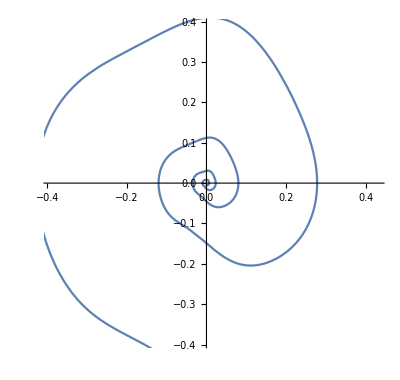

```mathematica
ClearAll["Global`*"];
ϵ=0.16;
γ=0.4;
ω=0.97;
L=1+ϵ Sin[ω*t+9π/8]^7;
a=7ϵ*ω Sin[ω*t+9π/8]^6 Cos[ω*t+9π/8];

{y1sol,y2sol}=NDSolveValue[{y'[t]==x[t],x'[t]==-(2/L*a+γ L)*x[t]-1/L*Sin[y[t]],y[0]==-1,x[0]==1},{y[t],x[t]},{t,0,30}]
ParametricPlot[{y1sol,y2sol},{t,0,30}]
```